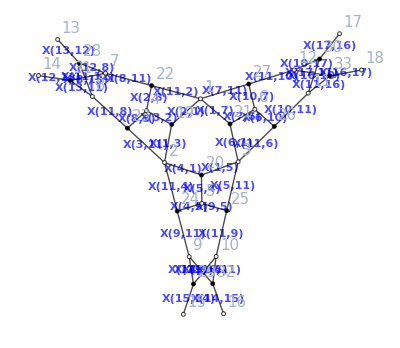

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=33;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
(*This is to fix my functional tests*)
```

```mathematica
Map[DeleteDuplicates,Map[#[[1]]/#[[2]]&,zigZagsAsPerfectMatchings[a,b,c,d],{2}]]
```

{{(X[1,5] X[2,4] X[3,5] X[6,2] X[6,9] X[7,3] X[8,9])/(X[1,6] X[2,7] X[3,8] X[4,3] X[5,2] X[5,9])},{(X[2,1] X[3,8] X[5,9] X[7,6])/(X[1,5] X[6,2] X[8,7] X[9,3])},{(X[3,2] X[4,5] X[8,7])/(X[2,4] X[7,3])},{(X[1,6] X[5,2])/(X[2,1] X[4,5] X[6,9])},{(X[2,7] X[4,3])/(X[3,2] X[5,4] X[7,6])},{(X[5,4] X[9,3])/(X[3,5] X[8,9])}}

```mathematica
And@@Map[Length[#]==1&,yieldedzigzags]
```

True

```mathematica
yieldedzigzags
```

{{(X[2,9] X[6,7])/(X[7,2] X[9,8])},{(X[3,10] X[7,6])/(X[6,3] X[10,9])},{(X[1,4] X[8,10])/(X[10,1] Y[4,5])},{(X[2,5] X[4,5] X[9,3] X[9,8] X[10,1] X[10,6])/(X[1,8] X[2,9] X[3,10] X[4,10] X[5,6])},{(X[3,7] X[10,9])/(X[7,6] X[9,3])},{(X[1,8] Y[4,5])/(X[5,1] X[8,10])},{X[5,6]/(X[4,5] X[6,7])},{(X[4,10] X[5,1] X[6,3] X[7,2])/(X[1,4] X[2,5] X[3,7] X[10,6])}}

```mathematica
zigzags=makeZigZags[a,b,c,d]
```

{(X[1,2] X[2,1] X[3,4] X[4,3] Y[3,4])/(X[3,1] X[4,2] Y[1,4] Y[2,3]),(X[1,4] X[2,3] Y[3,1] Y[4,2])/(X[1,2] X[2,1] X[3,4] X[4,3] Y[3,4]),(X[3,1] X[4,2])/(X[1,4] X[2,3]),(Y[1,4] Y[2,3])/(Y[3,1] Y[4,2])}

```mathematica
yieldedzigzags=Map[DeleteDuplicates,Map[#[[1]]/#[[2]]&,zigZagsAsPerfectMatchings[a,b,c,d],{2}]]
```

{{(X[1,2] X[2,1] X[3,4] X[4,3] Y[3,4])/(X[3,1] X[4,2] Y[1,4] Y[2,3])},{(X[1,4] X[2,3] Y[3,1] Y[4,2])/(X[1,2] X[2,1] X[3,4] X[4,3] Y[3,4])},{(X[3,1] X[4,2])/(X[1,4] X[2,3])},{(Y[1,4] Y[2,3])/(Y[3,1] Y[4,2])}}

```mathematica
And@@MapThread[#1===#2||#1==={}&,{yieldedzigzags,Transpose[{zigzags}]}]
```

True